```mathematica
R=1/2((a-x0)^2+b(x1-x0^2)^2)
f=FullSimplify@D[R,{{x0,x1}}]
f={-a +x0+2b x0^3-2b x0 x1,b(-x0^2+x1)}
J=D[f,{{x0,x1}}]
```

1/2 ((a-x0)^2+b (-x0^2+x1)^2)

{-a+x0+2 b x0^3-2 b x0 x1,b (-x0^2+x1)}

{-a+x0+2 b x0^3-2 b x0 x1,b (-x0^2+x1)}

{{1+6 b x0^2-2 b x1,-2 b x0},{-2 b x0,b}}

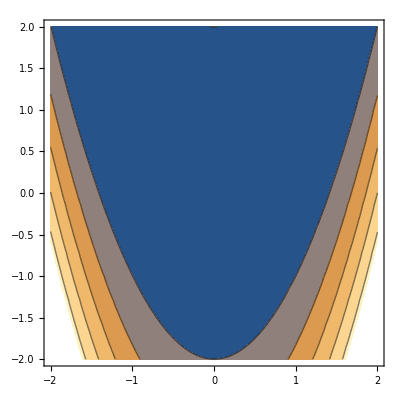

```mathematica
ContourPlot[R/.{a->1,b->100},{x0,-2,2},{x1,-2,2}]
```

```mathematica
NSolve[f==0/.{a->1,b->100},{x0,x1}]
R/.%
```

{{x0→1.,x1→1.}}

{1/2 (0.+(-1.+a)^2)}